```mathematica
(* 提取数据集中的部分元素 *)
Part[{1,2,3,4},4]
```

4

```mathematica
(* Part指令的快捷表示 [[]] *)
{10,100,1000,1000}[[4]]
```

1000

```mathematica
(* 使用转移序列输入[[]] *)
{10,20,30,40}⟦4⟧
```

40

```mathematica
(* 嵌套列表 *)
listOfScores = Import["http://www.handsonstart.com/ExampleDataScores.txt","Data"]
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}}

```mathematica
listOfScores[[1]]
```

{Joe,Smith,94}

```mathematica
listOfScores[[1,3]]  (* 这里类似于Python语言中的索引 *)
```

94

```mathematica
TableForm[listOfScores]
```

Joe | Smith | 94
Jane | Smith | 85
Bob | Example | 82
Bill | Student | 83
Michelle | Abacus | 98

```mathematica
TraditionalForm[listOfScores]
```

(Joe | Smith | 94
Jane | Smith | 85
Bob | Example | 82
Bill | Student | 83
Michelle | Abacus | 98)

```mathematica
(* 提取某一行上的全部数据 *)
listOfScores[[3,All]]
```

{Bob,Example,82}

```mathematica
(* 提取某一列上的全部数据 *)
listOfScores[[All,3]]
```

{94,85,82,83,98}

```mathematica
(* 提取子矩阵 *)
{2,10,100,1000,2000}[[2;;4]]
```

{10,100,1000}

```mathematica
TableForm[listOfScores]
```

Joe | Smith | 94
Jane | Smith | 85
Bob | Example | 82
Bill | Student | 83
Michelle | Abacus | 98

```mathematica
listOfScores[[All,1;;2]] (* 切片的记号是;; *)
```

{{Joe,Smith},{Jane,Smith},{Bob,Example},{Bill,Student},{Michelle,Abacus}}

```mathematica
(* 以数据列表的形式进行数据的提取 *)
listOfScores[[All,{1,2,3}]]
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}}

```mathematica
MatrixForm[{{"Joe","Smith",94},{"Jane","Smith",85},{"Bob","Example",82},{"Bill","Student",83},{"Michelle","Abacus",98}}]
```

(Joe | Smith | 94
Jane | Smith | 85
Bob | Example | 82
Bill | Student | 83
Michelle | Abacus | 98)

```mathematica
(* 修改矩阵中的某些值 *)
listOfScores[[4]]= {"New","Entry",48}
```

{New,Entry,48}

```mathematica
listOfScores
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98}}

```mathematica
MatrixForm[listOfScores]
```

(Joe | Smith | 94
Jane | Smith | 85
Bob | Example | 82
New | Entry | 48
Michelle | Abacus | 98)

```mathematica
listOfScores[[2,3]] = 88 (* 对某一个元素的修改 *)
```

88

```mathematica
listOfScores
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98}}

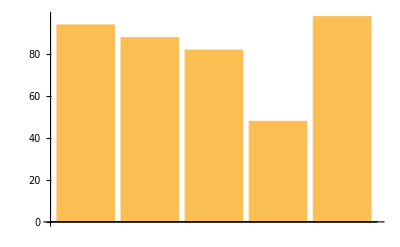

```mathematica
(* 基于数据的提取进行图形的绘制 *)
BarChart[listOfScores[[All,3]]]
```

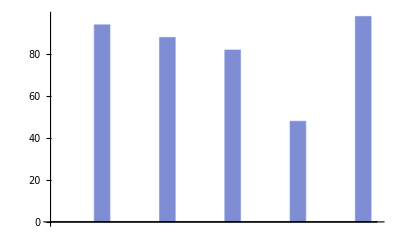

```mathematica
BarChart[listOfScores[[All]]] (* 不恰当的绘图指令会导致绘图结果与我们想要的相去甚远 *)
```

```mathematica
(* 有关于工作表的问题 *)
Import["ExampleData/elements.xls"]
```

{{{AtomicNumber,Abbreviation,Name,AtomicWeight},{1.,H,Hydrogen,1.00793},{2.,He,Helium,4.00259},{3.,Li,Lithium,6.94141},{4.,Be,Beryllium,9.01218},{5.,B,Boron,10.8086},{6.,C,Carbon,12.0107},{7.,N,Nitrogen,14.0067},{8.,O,Oxygen,15.9961},{9.,F,Fluorine,18.9984}}}

```mathematica
Dimensions[%]
```

{1,10,4}

```mathematica
(* 取得第一张工作表 *)
Import["ExampleData/elements.xls"][[1]]
```

{{AtomicNumber,Abbreviation,Name,AtomicWeight},{1.,H,Hydrogen,1.00793},{2.,He,Helium,4.00259},{3.,Li,Lithium,6.94141},{4.,Be,Beryllium,9.01218},{5.,B,Boron,10.8086},{6.,C,Carbon,12.0107},{7.,N,Nitrogen,14.0067},{8.,O,Oxygen,15.9961},{9.,F,Fluorine,18.9984}}

```mathematica
Dimensions[%]
```

{10,4}

```mathematica
Import["ExampleData/elements.xls",{"Data",1}]
```

{{AtomicNumber,Abbreviation,Name,AtomicWeight},{1.,H,Hydrogen,1.00793},{2.,He,Helium,4.00259},{3.,Li,Lithium,6.94141},{4.,Be,Beryllium,9.01218},{5.,B,Boron,10.8086},{6.,C,Carbon,12.0107},{7.,N,Nitrogen,14.0067},{8.,O,Oxygen,15.9961},{9.,F,Fluorine,18.9984}}

```mathematica
Import["ExampleData/elements.xls"]
```

{{{AtomicNumber,Abbreviation,Name,AtomicWeight},{1.,H,Hydrogen,1.00793},{2.,He,Helium,4.00259},{3.,Li,Lithium,6.94141},{4.,Be,Beryllium,9.01218},{5.,B,Boron,10.8086},{6.,C,Carbon,12.0107},{7.,N,Nitrogen,14.0067},{8.,O,Oxygen,15.9961},{9.,F,Fluorine,18.9984}}}

```mathematica
Dimensions[Import["ExampleData/elements.xls",{"Data",1}]]
```

{10,4}

```mathematica
(* 改变列表的结构 *)
newScores = {
	listOfScores,
	{
		{"Michael","Morrison",95},
		{"kelvin","Mischol",96},
		{"Cliff","Hastings",99}
       }
}
```

{{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98}},{{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}}}

```mathematica
MatrixForm[newScores]
```

({{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98}}
{{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}})

```mathematica
newScores[[1,2]]
```

{Jane,Smith,88}

```mathematica
newScores[[All,2]]
```

{{Jane,Smith,88},{kelvin,Mischol,96}}

```mathematica
(* 使用[[]]来对姓氏进行提取 *)
newScores[[1,1,2]]
```

Smith

```mathematica
newScores[[2,1,2]]
```

Morrison

```mathematica
(* 以手动和繁琐的形式对所有的姓氏进行提取 *)
{
	newScores[[1,1,2]],
	newScores[[1,2,2]],
	newScores[[1,3,2]],
	newScores[[1,4,2]],
	newScores[[1,5,2]],
	newScores[[2,1,2]],
	newScores[[2,2,2]],
	newScores[[2,3,2]]
}
```

{Smith,Smith,Example,Entry,Abacus,Morrison,Mischol,Hastings}

```mathematica
(* 使用Flatte对数据进行平坦化 *)
Flatten[newScores]
```

{Joe,Smith,94,Jane,Smith,88,Bob,Example,82,New,Entry,48,Michelle,Abacus,98,Michael,Morrison,95,kelvin,Mischol,96,Cliff,Hastings,99}

```mathematica
(* 其中newScores的形式为 *)
newScores
```

{{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98}},{{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}}}

```mathematica
(* 使用Partition从一维列表中创建二维列表 *)
Partition[{1,2,3,4,5,6},2](* 第二个参数表示多少列 *)
```

{{1,2},{3,4},{5,6}}

```mathematica
(* 对学生数据进行清理 *)
```

```mathematica
cleanedNewScores = Partition[Flatten[newScores],3] (* 将元素划分为三列 *)
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}}

```mathematica
Partition[Flatten[listOfScores[[All,1;;2]]],5] (* 后面的那个参数指的是每一个小划分里面具有多少个元素 *)
```

{{Joe,Smith,Jane,Smith,Bob},{Example,New,Entry,Michelle,Abacus}}

```mathematica
MatrixForm[listOfScores]
```

(Joe | Smith | 94
Jane | Smith | 88
Bob | Example | 82
New | Entry | 48
Michelle | Abacus | 98)

```mathematica
cleanedNewScores[[All,2]]
```

{Smith,Smith,Example,Entry,Abacus,Morrison,Mischol,Hastings}

```mathematica
(* 删除元素 *)
Drop[cleanedNewScores,2] (* 删除cleanedNewScores的前两个元素 *)
```

{{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}}

```mathematica
Drop[cleanedNewScores,None,1] (* 去掉列表中的第一列 *)
```

{{Smith,94},{Smith,88},{Example,82},{Entry,48},{Abacus,98},{Morrison,95},{Mischol,96},{Hastings,99}}

```mathematica
(* 取得学生分数表格的第二列与第三列 *)
cleanedNewScores
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}}

```mathematica
cleanedNewScores[[All,{2,3}]]
```

{{Smith,94},{Smith,88},{Example,82},{Entry,48},{Abacus,98},{Morrison,95},{Mischol,96},{Hastings,99}}

```mathematica
MatrixForm[{{"Smith",94},{"Smith",88},{"Example",82},{"Entry",48},{"Abacus",98},{"Morrison",95},{"Mischol",96},{"Hastings",99}}]
```

(Smith | 94
Smith | 88
Example | 82
Entry | 48
Abacus | 98
Morrison | 95
Mischol | 96
Hastings | 99)

```mathematica
(* 将新元素临时加入列表当中 *)
AppendTo[cleanedNewScores,{"Jill","New",90}]
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}}

```mathematica
cleanedNewScores
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}}

```mathematica
MatrixForm[%]
```

(Joe | Smith | 94
Jane | Smith | 88
Bob | Example | 82
New | Entry | 48
Michelle | Abacus | 98
Michael | Morrison | 95
kelvin | Mischol | 96
Cliff | Hastings | 99
Jill | New | 90)

```mathematica
(* 合并字符串 *)
StringJoin[cleanedNewScores[[1,1]]," ",cleanedNewScores[[1,2]]]
```

Joe Smith

```mathematica
StringJoin["Joe","Smith"]
```

JoeSmith

```mathematica
Table[
	StringJoin[cleanedNewScores[[i,1]]," ",cleanedNewScores[[i,2]]],
	{i,1,Length[cleanedNewScores]}
]
```

{Joe Smith,Jane Smith,Bob Example,New Entry,Michelle Abacus,Michael Morrison,kelvin Mischol,Cliff Hastings,Jill New}

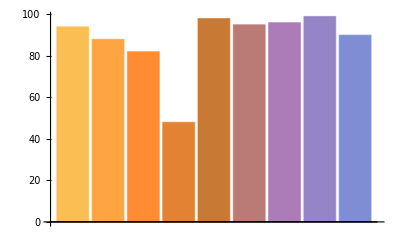

```mathematica
(* 依据数据进行图像的绘制 *)
BarChart[{cleanedNewScores[[All,3]]}]
```

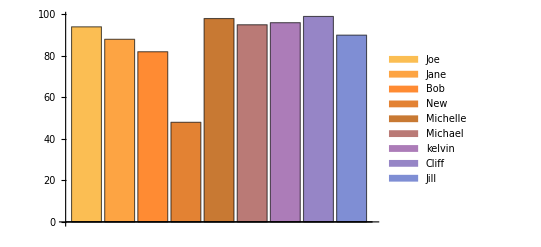

```mathematica
(* 为上述图像添加图例 *)
BarChart[{cleanedNewScores[[All,3]]},ChartLegends->cleanedNewScores[[All,1]]] (* 这里必须将每一个元素都选择为单独的子列表 *)
```

```mathematica
cleanedNewScores[[All,3]]
```

{94,88,82,48,98,95,96,99,90}

```mathematica
{cleanedNewScores[[All,3]]}
```

{{94,88,82,48,98,95,96,99,90}}

```mathematica
(* 测试 如果一个列表不加大括号，那么绘制出来的图形将无法区分图例 *)
```

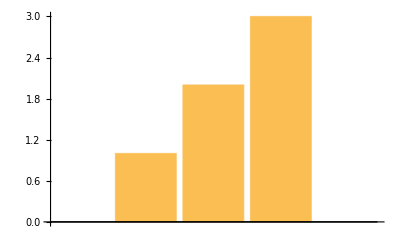

```mathematica
BarChart[{1,2,3}]
```

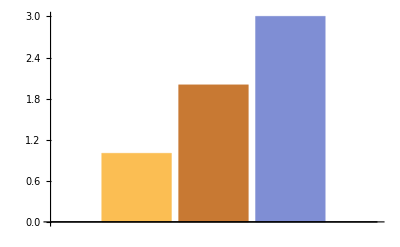

```mathematica
BarChart[{{1,2,3}}]
```

```mathematica
(* 排序和模式匹配 *)
cleanedNewScores
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}}

```mathematica
MatrixForm[{{"Joe","Smith",94},{"Jane","Smith",88},{"Bob","Example",82},{"New","Entry",48},{"Michelle","Abacus",98},{"Michael","Morrison",95},{"kelvin","Mischol",96},{"Cliff","Hastings",99},{"Jill","New",90}}]
```

(Joe | Smith | 94
Jane | Smith | 88
Bob | Example | 82
New | Entry | 48
Michelle | Abacus | 98
Michael | Morrison | 95
kelvin | Mischol | 96
Cliff | Hastings | 99
Jill | New | 90)

```mathematica
Sort[cleanedNewScores]
```

{{Bob,Example,82},{Cliff,Hastings,99},{Jane,Smith,88},{Jill,New,90},{Joe,Smith,94},{kelvin,Mischol,96},{Michael,Morrison,95},{Michelle,Abacus,98},{New,Entry,48}}

```mathematica
MatrixForm[{{"Bob","Example",82},{"Cliff","Hastings",99},{"Jane","Smith",88},{"Jill","New",90},{"Joe","Smith",94},{"kelvin","Mischol",96},{"Michael","Morrison",95},{"Michelle","Abacus",98},{"New","Entry",48}}]
```

(Bob | Example | 82
Cliff | Hastings | 99
Jane | Smith | 88
Jill | New | 90
Joe | Smith | 94
kelvin | Mischol | 96
Michael | Morrison | 95
Michelle | Abacus | 98
New | Entry | 48)

```mathematica
Sort[cleanedNewScores[[All,3]]]
```

{48,82,88,90,94,95,96,98,99}

```mathematica
(* 根据待排序元素的最后一个指标进行排序 *)
SortBy[cleanedNewScores,Last]
```

{{New,Entry,48},{Bob,Example,82},{Jane,Smith,88},{Jill,New,90},{Joe,Smith,94},{Michael,Morrison,95},{kelvin,Mischol,96},{Michelle,Abacus,98},{Cliff,Hastings,99}}

```mathematica
MatrixForm[{{"New","Entry",48},{"Bob","Example",82},{"Jane","Smith",88},{"Jill","New",90},{"Joe","Smith",94},{"Michael","Morrison",95},{"kelvin","Mischol",96},{"Michelle","Abacus",98},{"Cliff","Hastings",99}}]
```

(New | Entry | 48
Bob | Example | 82
Jane | Smith | 88
Jill | New | 90
Joe | Smith | 94
Michael | Morrison | 95
kelvin | Mischol | 96
Michelle | Abacus | 98
Cliff | Hastings | 99)

```mathematica
(* 依据自定义规则进行排序 *)
sortFun[x_] := StringLength[x[[1]]];
MatrixForm[cleanedNewScores]
```

(Joe | Smith | 94
Jane | Smith | 88
Bob | Example | 82
New | Entry | 48
Michelle | Abacus | 98
Michael | Morrison | 95
kelvin | Mischol | 96
Cliff | Hastings | 99
Jill | New | 90)

```mathematica
SortBy[cleanedNewScores,sortFun]
```

{{Bob,Example,82},{Joe,Smith,94},{New,Entry,48},{Jane,Smith,88},{Jill,New,90},{Cliff,Hastings,99},{kelvin,Mischol,96},{Michael,Morrison,95},{Michelle,Abacus,98}}

```mathematica
MatrixForm[{{"Bob","Example",82},{"Cliff","Hastings",99},{"Jane","Smith",88},{"Jill","New",90},{"Joe","Smith",94},{"kelvin","Mischol",96},{"Michael","Morrison",95},{"Michelle","Abacus",98},{"New","Entry",48}}]
```

(Bob | Example | 82
Cliff | Hastings | 99
Jane | Smith | 88
Jill | New | 90
Joe | Smith | 94
kelvin | Mischol | 96
Michael | Morrison | 95
Michelle | Abacus | 98
New | Entry | 48)

```mathematica
(* Reverse用于返回逆序列表 *)
(* 对考试分数进行降序排列 *)
Reverse[SortBy[newScores,Last]]
```

{{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98}},{{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}}}

```mathematica
(* 使用Head来获取数据类型 *)
Head[1]
```

Integer

```mathematica
Head[1.5]
```

Real

```mathematica
SymbolName[Real]
```

Real

```mathematica
Head[{1,2,3}]
```

List

```mathematica
(* 使用Case来基于标头进行对列表中的元素进行筛选 *)
Cases[{1,2,3,4,5,6,7,8,9,0,1.1,2.2,3.3},_Real]
```

{1.1,2.2,3.3}

```mathematica
Cases[{1,2,3,4,5,6,7,8,9,0,1.1,2.2,3.3},_Integer]
```

{1,2,3,4,5,6,7,8,9,0}

```mathematica
Cases[{1,2,3,4,5,6,7,8,9,0,1.1,2.2,3.3},_String]
```

{}

```mathematica
(* 使用Case进行对考试成绩进行提取 *)
Cases[Flatten[newScores],_Integer]
```

{94,88,82,48,98,95,96,99}

```mathematica
(* AppendTo的使用 *)
```

```mathematica
cleanedNewScores
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}}

```mathematica
AppendTo[cleanedNewScores,{"Bad","Data","Here"}]
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90},{Bad,Data,Here}}

```mathematica
Cases[cleanedNewScores,{_,_,_Integer}]  (* 使用模式匹配的方法来寻找元素 *)
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}}

```mathematica
MatrixForm[{{"Joe","Smith",94},{"Jane","Smith",88},{"Bob","Example",82},{"New","Entry",48},{"Michelle","Abacus",98},{"Michael","Morrison",95},{"kelvin","Mischol",96},{"Cliff","Hastings",99},{"Jill","New",90}}]
```

(Joe | Smith | 94
Jane | Smith | 88
Bob | Example | 82
New | Entry | 48
Michelle | Abacus | 98
Michael | Morrison | 95
kelvin | Mischol | 96
Cliff | Hastings | 99
Jill | New | 90)

```mathematica
(* 筛选出具有特殊模式的子表 *)
Cases[cleanedNewScores,{_,_,_Integer}]
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}}

```mathematica
newScores
```

{{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98}},{{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}}}

```mathematica
cleanedNewScores
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90},{Bad,Data,Here}}

```mathematica
cleanedNewScores /. {"Missing"} -> Nothing
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90},{Bad,Data,Here}}

```mathematica
(* 使用select来对数据进行筛选 *)
selectFunc[x_] :=Length[x]==3;
Select[cleanedNewScores,selectFunc]
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90},{Bad,Data,Here}}

```mathematica
cleanedNewScores
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90},{Bad,Data,Here}}

```mathematica
selectFunc2[x_] := And[x[[2]]=="Smith",x[[3]]>=90];
Select[cleanedNewScores,selectFunc2]
```

{{Joe,Smith,94}}

```mathematica
selectFunc2[x_]:=And[x[[2]]=="Smith",x[[3]]>=90];
Select[Cases[cleanedNewScores,{_,_String,_Integer}],selectFunc2]
```

{{Joe,Smith,94}}

```mathematica
selectFunc3[x_]:=Or[x[[3]]<85,x[[3]]>95];
Select[Cases[cleanedNewScores,{_,_String,_Integer}],selectFunc3]
```

{{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{kelvin,Mischol,96},{Cliff,Hastings,99}}

```mathematica
(* 使用Wolfram内置的指令与Select一起进行数据筛选 *)
Select[Flatten[cleanedNewScores],NumberQ]
```

{94,88,82,48,98,95,96,99,90}

```mathematica
Select[Flatten[cleanedNewScores],EvenQ]
```

{94,88,82,48,98,96,90}

```mathematica
Select[Flatten[cleanedNewScores],GreaterThan[90]]
```

{94,98,95,96,99}

```mathematica
(* 数据操作函数与Manipulate一起使用 *)
```

```mathematica
manipulateData=Cases[cleanedNewScores,{_String,_String,_Integer}]
```

{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{New,Entry,48},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}}

```mathematica
MatrixForm[manipulateData] (* 数据集的制作 *)
```

(Joe | Smith | 94
Jane | Smith | 88
Bob | Example | 82
New | Entry | 48
Michelle | Abacus | 98
Michael | Morrison | 95
kelvin | Mischol | 96
Cliff | Hastings | 99
Jill | New | 90)

```mathematica
scoreList = Table[(
selectFun4[val_]:=val[[3]]>=score;
Select[manipulateData,selectFun4]
),
{score,70,100,1}
];
scoreList
```

{{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Bob,Example,82},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Jane,Smith,88},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99},{Jill,New,90}},{{Joe,Smith,94},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}},{{Joe,Smith,94},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}},{{Joe,Smith,94},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}},{{Joe,Smith,94},{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}},{{Michelle,Abacus,98},{Michael,Morrison,95},{kelvin,Mischol,96},{Cliff,Hastings,99}},{{Michelle,Abacus,98},{kelvin,Mischol,96},{Cliff,Hastings,99}},{{Michelle,Abacus,98},{Cliff,Hastings,99}},{{Michelle,Abacus,98},{Cliff,Hastings,99}},{{Cliff,Hastings,99}},{}}

```mathematica
Manipulate[BarChart[scoreList[[i]][[All,3]]],{i,1,30,1},SaveDefinitions->True]
```

Part::partd: 部分指定 scoreList⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 scoreList⟦1⟧⟦All,3⟧ 比对象深度更长.

Part::partd: 部分指定 scoreList⟦1,All,3⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

BarChart::ldata: scoreList⟦1⟧⟦All,3⟧ 不是一个有效的数据集或者数据集列表.

Part::partd: 部分指定 scoreList⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 scoreList⟦1⟧⟦All,3⟧ 比对象深度更长.

Part::partd: 部分指定 scoreList⟦1,All,3⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

BarChart::ldata: scoreList⟦1⟧⟦All,3⟧ 不是一个有效的数据集或者数据集列表.

Part::partd: 部分指定 scoreList⟦4⟧ 比对象深度更长.

Part::partd: 部分指定 scoreList⟦4⟧⟦All,3⟧ 比对象深度更长.

Part::partd: 部分指定 scoreList⟦4,All,3⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

BarChart::ldata: scoreList⟦4⟧⟦All,3⟧ 不是一个有效的数据集或者数据集列表.

Part::partd: 部分指定 scoreList⟦13⟧ 比对象深度更长.

Part::partd: 部分指定 scoreList⟦13⟧⟦All,3⟧ 比对象深度更长.

Part::partd: 部分指定 scoreList⟦13,All,3⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

BarChart::ldata: scoreList⟦13⟧⟦All,3⟧ 不是一个有效的数据集或者数据集列表.

```mathematica
(* 用关联组织数据 类似键值对 *)
myAssoc = Association[
{"Cliff"->99,"Kelvin"->96,"Michael"->95}
];
```

```mathematica
myAssoc["Michael"]
```

95

```mathematica
(* 可以使用 <||>来输入关联 *)
myAssoc2 = <| "Tasha" -> "Florida","Kathy"->"Arizona"|>;
```

```mathematica
myAssoc2["Tasha"]
```

Florida

```mathematica
(* 将listOfSource定义为原始值 *)
listOfScores = Import["http://www.handsonstart.com/ExampleDataScores.txt","Data"]
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}}

```mathematica
listOfScores
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}}

```mathematica
scoreAssoc = AssociationThread[listOfScores[[All]][[All,1]],listOfScores[[All]][[All,3]]](* 在学生的姓氏与分数之间建立关联 *)
```

<|Joe→94,Jane→85,Bob→82,Bill→83,Michelle→98|>

```mathematica
(*
	关于下标的一些说法：
		listOfSource[[All]][[1]]是指整个列表被选中([[All]])以后第一个元素，即为 <|"Joe"->94|>
	   listOfSource[[All,1]]是指整个列表被选中以后，第一列元素，在[[]]内部写出的下标组合才是选取多维数组元素的正确写法
*)
```

```mathematica
listOfScores
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}}

```mathematica
listOfScores[[All]]
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}}

```mathematica
listOfScores[[All,1]]
```

{Joe,Jane,Bob,Bill,Michelle}

```mathematica
AssociationThread[listOfScores[[All,1]],listOfScores[[All,3]]]
```

<|Joe→94,Jane→85,Bob→82,Bill→83,Michelle→98|>

```mathematica
scoreAssoc["Bill"]
```

83

```mathematica
scoreAssoc["Micheal"]
```

Missing[KeyAbsent,Micheal]

```mathematica
scoreAssoc["Michelle"]
```

98

```mathematica
Sort[Values[scoreAssoc]]
```

{82,83,85,94,98}

```mathematica
Sort[Keys[scoreAssoc]]
```

{Bill,Bob,Jane,Joe,Michelle}

```mathematica
(* 使用DataSet来显示具有键值对形式的数据结构的结构化数据集 *)
Dataset[scoreAssoc]
```

```mathematica
(* 获取上一层输出的底层数据 *)
Normal[DateSet[scoreAssoc]]
```

DateSet[{Joe→94,Jane→85,Bob→82,Bill→83,Michelle→98}]

```mathematica
Normal[scoreAssoc]
```

{Joe→94,Jane→85,Bob→82,Bill→83,Michelle→98}

```mathematica
TableForm[List@@@{"Joe"->94,"Jane"->85,"Bob"->82,"Bill"->83,"Michelle"->98}]
```

Joe | 94
Jane | 85
Bob | 82
Bill | 83
Michelle | 98

```mathematica
titanic = ExampleData[{"Dataset","Titanic"}]
```

```mathematica
ExampleData["Dataset"]
```

{{Dataset,Planets},{Dataset,StatePopulations},{Dataset,Titanic}}

```mathematica
titanic[[All,"age"]]
```

```mathematica
(* 删除缺失值 *)
DeleteMissing[%]
```

```mathematica
N[Mean[DeleteMissing[titanic[[All,"age"]]]]]
```

29.9006

```mathematica
Clear[listOfScores,newScores,cleanedNewScores,sortFun,selectFunc,selectFunc2,selectFunc3,selectFunc4,selectFun4,manipulateData,myAssoc,myAssoc2,scoreAssoc,scoreList,score]
```